```mathematica
V[r_]:=-e^2/(4*π*ϵ0*r); (* r Angstrom-etan *)
e=1.602177*10^-19 ;(*Coulomb*) 
ϵ0=8.854187*10^-12; (*C^2 /(N m^2)*)
AToM=10^-10; (*A -> m-tara pasatzeko *) 
JtoeV=6.242*10^18; (* J-etail -> eV-etara pasazteko*)

V[1]
```

```mathematica
-2.3070788181819784*^-28

JtoeV*V[1*AToM]
```

-2.30708×10^-28

-14.4008

```mathematica
e=1;
ϵ0=1/(4*π) ;(* 4*π*ϵ0=1 *) 
AtoBohr=1.88973*1;
N[V[1*AtoBohr]]
```

-0.529176

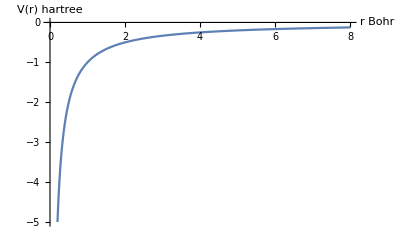

```mathematica
-0.5291761256899133

Plot[V[r],{r,0,8},PlotRange->{-5,0},AxesLabel->{"r Bohr","V(r) hartree"}]
```